# Lab 2: Defining Functions Assignment

### Instructions

Welcome to the assignment for Lab 2. The purpose of this assignment is to assess your ability to define and use functions in Mathematica. Some things to remember as you complete this assignment:
1. Save the notebook to your computer right away, and save your work often. 
2. When you have finished all the exercises, close any unnecessary cells and save as a PDF.
3. Upload the PDF on Canvas.
4. Do not delete this notebook. Save all your work until after the semester is over and your final grade has been issued.

### Question 1: Defining a Function

a) In the cell below, define the following values: let “a” equal the number of letters in your first name, and let “b” equal the number of letters in your last name.

```mathematica
a = StringLength["Caleb"];
b = StringLength["Jacobs"];
```

b) Define the function g(x) to be 3 x^2+5x-2. Then, evaluate g(2).

```mathematica
g[x_]=3 x^2+5x-2;
g[2]
```

20

c) Plot the function “g” from “- a” to “b”. You must use the variables and not the actual values in your plot command.

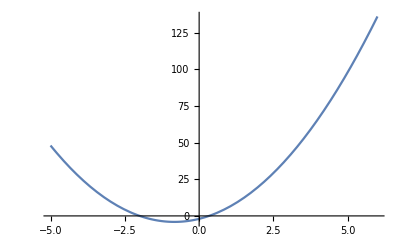

```mathematica
Plot[g[x],{x,-a,b}]
```

### Question 2: Working with Multiple Functions

a) Define a new function to be tan(x)-√x (note that the command for √x is Sqrt[ ], but you can also get the symbol by pressing ctrl+2 or you can find it in the palette). Use your last name as the name of this function.

```mathematica
jacobs[x_] = Tan[x]-√x
```

-√x+Tan[x]

b) Evaluate the function “lastname” at x=π/4 (Recalling that tan(π/4)=1 will help you check if your answer looks correct). Present your answer as a decimal.

```mathematica
jacobs[π/4]//N
```

0.113773

c) Define a function “func” to be ln(x) + x^2+x. Evaluate “func” at x=1.

```mathematica
func[x_]=Log[x]+x^2+x;
func[1]
```

2

d) Plot “func” using the interval x=-4 to x=0. Create a text cell below, and explain why the plot is not visible.

```mathematica
Plot[func[x],{x,-4,0}]
```

-Graphics-

Log of a negative value returns a complex number and can’t be plotted on the real number line

e) In general, the composition of functions is not commutative. Recall that if we have two functions g(x) and f(x), and if f ◦ g = g ◦ f for any input, then we say that g and f are commutative.

Are your functions from Question 2 commutative at x=1.5? Evaluate the composition of your two functions “lastname” and “func” in different orders at x=1.5, i.e. calculate func[lastname[1.5]] and lastname[func[1.5]]. Create a text cell stating whether or not your calculations support the statement that the composition of functions is not commutative.

```mathematica
jacobs[func[1.5]]==func[jacobs[1.5]]
```

False

The logical test of each composition order comes out false showing that the functions are not commutative and that they don’t return the same value given the same argument.